```mathematica
.3/.5
```

0.6

```mathematica
B=140*10^(-6)
B=10^(-3)
R=0.25*pc
R=2*pc
A=Pi*R^2
result=B*A/(pc^2)
result/10^(-4)
```

7/50000

1/1000

7.715×10^17

6.172×10^18

1.19675×10^38

0.0125664

125.664

```mathematica
B=2.5*10^(-6)
R=100*pc
A=Pi*R^2
result=B*A/(pc^2)
```

2.5×10^-6

3.086×10^20

2.99186×10^41

0.0785398

```mathematica
M=15*msun
rg=G*M/c^2
tg=rg/c
omegak=(r/rg)^(-3/2)/tg
fk=omegak/(2*Pi)
tauk=1/fk
```

2.9835×10^34

2.21483×10^6

0.0000738788

(4.4616×10^13)/r^(3/2)

(7.10086×10^12)/r^(3/2)

1.40828×10^-13 r^(3/2)

```mathematica
sols=Solve[fk==100,r]
(r/rg)/.sols[[1]]
```

{{r→1.71478×10^7}}

7.74224

```mathematica
ff=100*tg
tf=1/ff
```

0.00738788

135.357

```mathematica
ff=300*tg
tf=1/ff
```

0.0221636

45.1189

```mathematica
44*12
```

528

```mathematica
60*12+151.91
```

871.91

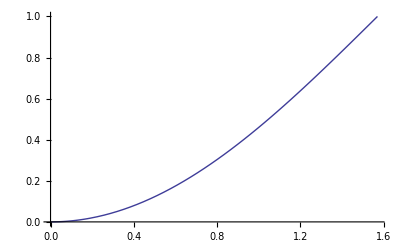

```mathematica
Plot[1-Cos[h],{h,0,Pi/2}]
```

```mathematica
Clear[h]
mu=4
nu=3/4
r0=4
r=2
fm=1-Cos[h]^mu
fp=1+Cos[h]^mu
Aphid=(1/2)*((r+r0)^nu*fm+2*fp*(1-Log[fp]))
Aphidalt=Aphid//.{h->Pi-hp}
Aphidalt=Aphidalt//.{hp->h}
Aphidgen=If[h<Pi/2,Aphid,Aphidalt]
```

4

3/4

4

2

1-Cos[h]^4

1+Cos[h]^4

1/2 (6^(3/4) (1-Cos[h]^4)+2 (1+Cos[h]^4) (1-Log[1+Cos[h]^4]))

1/2 (6^(3/4) (1-Cos[hp]^4)+2 (1+Cos[hp]^4) (1-Log[1+Cos[hp]^4]))

1/2 (6^(3/4) (1-Cos[h]^4)+2 (1+Cos[h]^4) (1-Log[1+Cos[h]^4]))

If[h<π/2,Aphid,Aphidalt]

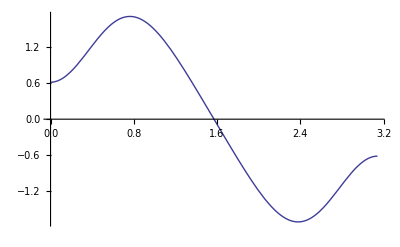

```mathematica
Plot[Aphidgen*Cos[h],{h,0,Pi}]
```